# MuRF project PIC functions

This notebook demonstrates various properties of the MuRF PIC code.
Copyright © Terje B. 2012

```mathematica
(* No need for a long history length eating memory *)
$HistoryLength=1;
ClearAll;
```

```mathematica
potpos=0;
resolution=0;
maxpotpos=10.0;
voltref=5.0;
offset=0;
potposorg=0;
peak=0;
percentrise=0;
percentfall=0;
startpos=0;
voltprsteprise=0;
voltprstepfall=0;
volt=0;
cutoff=0;
curvebreakpercent = 80;

GetPlotData[resolutionin_,potposin_] := Module[{},
curvedata=ConstantArray[0, resolutionin+1];
resolution=resolutionin;
potpos=potposin;
potposorg=potpos;
If [potposorg>maxpotpos /2.0, potpos=maxpotpos-potpos];
CreateRiseFallPercentCurve[potpos];
percentrise=(percentrise * resolution)/100.0;
percentfall=(percentfall * resolution)/100.0;
GetCutoffVoltForFallCurve[];
GetPeakPosInResolution[];

If [cutoff>0, startpos=0,startpos=peak-percentrise];

If [startpos<0, startpos=0];

If [percentrise==0, 
{
voltprsteprise=voltref;(*(voltref-cutoff)/1.0;*)
peak=0.0001;(*1.0;*)
},
voltprsteprise=(voltref-cutoff)/(peak-startpos);
];

voltprstepfall=voltref/percentfall;

If [voltprsteprise>voltref, voltprsteprise=voltref];

If [voltprstepfall>voltref, voltprstepfall=voltref];

(* START:This block is for each timer tick in PIC from 0 to resolution *)
For [counter=0,counter<=resolution,counter++,
If [potposorg>maxpotpos/2.0,
volt = GetVoltValue[resolution-counter],
volt = GetVoltValue[counter];
];
curvedata[[counter + 1]] = volt
];
(* END:This block is for each timer tick in PIC from 0 to resolution *)

curvedata
]
```

```mathematica
CreateRiseFallPercentCurve[potposin_]:=Module[{},
curvebreak=(maxpotpos / 2.0) * (curvebreakpercent / 100.0);
posrise=potposin;
posfall=potposin;
diprise=0;
dipfall=0;
ratiorise=0;
ratiofall=0;
advance=0;

If[potposin>curvebreak,
{
diprise=1.6;
dipfall=1.02;
advance=Abs[curvebreak-potposin];
ratiorise=(curvebreak-diprise);
posrise=curvebreak-(advance * ratiorise);
ratiofall=(curvebreak-dipfall);
posfall=curvebreak-(advance * ratiofall)
}
];

percentrise=(posrise * 1.9)^2;
percentfall=(posfall * 2.8)^2+1.0
]
```

```mathematica
GetPeakPosInResolution[]:=Module[{},
peak=(potpos^2/(maxpotpos / 2.0)) * (resolution / maxpotpos)
]
```

```mathematica
GetCutoffVoltForFallCurve[]:=Module[{},
voltprstepfall=(voltref/percentfall);
peak=GetPeakPosInResolution[];
If[resolution-peak-percentfall<0,
cutoff=Abs[resolution - peak  - percentfall] * voltprstepfall,
cutoff=0
]
]
```

```mathematica
GetVoltValue[resolutionpos_]:=Module[{},
If[resolutionpos<startpos,
volt=0,
{
If [resolutionpos<peak,
volt=(cutoff+(voltprsteprise*(resolutionpos-startpos)))^2/voltref,
{
If[resolutionpos≤peak+percentfall,
volt=(voltref-(voltprstepfall*(resolutionpos-peak)))^2/voltref,
volt=0
]
}
]; 
If [resolutionpos==Round[peak]&&volt<=voltref, volt=voltref]
 }
];
volt
]
```

Test the module:

{2.31098,126.44,57.76,32.,0,100,4,4,1.06812,1.06812}

{2.31098,126.44,57.76,32.,0,100,4.,6,1.06812,1.06812}

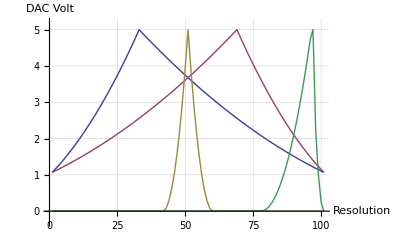

```mathematica
murfcurve1 = GetPlotData[100, 4];
{cutoff, percentfall, percentrise, peak, startpos, resolution, potpos, potposorg, murfcurve1[[1]], murfcurve1[[resolution+1]]}
murfcurve2 = GetPlotData[100, 6];
{cutoff, percentfall, percentrise, peak, startpos, resolution, potpos, potposorg, murfcurve2[[1]], murfcurve2[[resolution+1]]}
murfcurve3 = GetPlotData[100, 5];
murfcurve4 = GetPlotData[100, 8.5];

mplot1 = Show[ListLinePlot[{murfcurve1,murfcurve2,murfcurve3,murfcurve4},
PlotRange->{{0, resolution+1}, {-0.3, voltref+0.2}},
GridLines->Automatic, GridLinesStyle->LightGray,ImageSize->Scaled[.50],
 AxesLabel->{"Resolution", "DAC Volt"}]];

Grid[{{mplot1}}, Frame->All]
```

Animate and control the MuRF module with the MANIPULATE command:

```mathematica
Manipulate[
murfcurve = GetPlotData[theResolution, envelopePos];

mplot = Show[ListLinePlot[murfcurve,  PlotStyle->Blue, GridLines->Automatic, 
GridLinesStyle->LightGray, PlotRange->{{0, theResolution + 2}, {-0.3, voltref + 0.2}},
 Filling->Axis, PlotMarkers->Automatic],
AspectRatio->.35, ImageSize->Scaled[.98]];

Grid[{{mplot},{murfcurve}}, ItemSize->{{45}}, Spacings->{0.5,1.5}, Frame->All],
(* NOTE: theResolution = envelopePos = 5 creates curve problem *)
 {{theResolution, 50, "Max Elements"}, 6, 160, 1, Appearance->"Labeled"},
{{envelopePos, 0, "Envelope Position"}, 0, 10, 0.025, Appearance->"Labeled"},
 SaveDefinitions->True
]
```